```mathematica
πp[p_]:={p⟦1⟧,p⟦2⟧}/(p⟦3⟧+1);
πpInv[{a_,b_}]:={2*a,2*b,1+a^2+b^2}/(1-a^2-b^2);
πl[l_]:={l⟦1⟧,l⟦2⟧}/(-l⟦3⟧);
HNormalize[p_]:=p/Sqrt[Abs[-p⟦1⟧^2-p⟦2⟧^2+p⟦3⟧^2]];
angle[v_]:=Mod[Arg[v⟦1⟧+I*v⟦2⟧],2π];
line[{p1_,p2_}]:=Module[{p3},p3=Cross[p1,p2];HNormalize[p3]];
round[line_]:={NumberForm[line⟦1⟧,10],NumberForm[line⟦2⟧,10],line⟦3⟧};
label2color=Association[{"a"->Red,"b"->Blue,"c"->Purple,"d"->Brown}];
reflect[p_,L_]:=Module[{diff,dist,p2},dist=Norm[πp[p]-πl[L]]/Abs[-1/L⟦3⟧];p2=πl[L]-(πl[L]-πp[p])/dist^2;πpInv[p2]];
HSlinedrawArc[{{a_,b_,c_},{d_,e_,f_},label_},drawLabel_:True,drawColor_:True]:=Module[{L,radius,v1,v2,t1,t2,mint,maxt,txtloc,rg,color,ltscale},
L=line[{{a,b,c},{d,e,f}}];
If[Abs[L⟦3⟧]<0.0000001,radius=0,radius=Abs[-1/L⟦3⟧]];
v1=πp[{a,b,c}]-πl[L];
v2=πp[{d,e,f}]-πl[L];
t1=angle[v1];
t2=angle[v2];
mint=Min[t1,t2];
maxt=Max[t1,t2];
txtloc=(πl[L]-πp[{a,b,c}])+(πl[L]-πp[{d,e,f}]);
txtloc=πl[L]-txtloc/Norm[txtloc]*(radius+Min[0.15*radius,0.02]);
If[drawColor,color=label2color[label],color=Black];
ltscale=1-Max[Norm[πp[{a,b,c}]],Norm[πp[{d,e,f}]]];
rg={};
If[Abs[t1-t2]>π,maxt=maxt-2π];
If[Abs[L⟦3⟧]<0.0000001,rg={color,Thin,Line[{a,b}/(c+1),{d,e}/(f+1)]},rg={color,Thickness[Min[0.003,0.0001+0.005*√ltscale]],Circle[{L⟦1⟧,L⟦2⟧}/(-L⟦3⟧),radius,{mint,maxt}]}];
If[Norm[txtloc]<0.97&&drawLabel,rg=Append[rg,Text[Style[label,Black,FontFamily->"Cambria Math",FontSize->19-10*Max[(Norm[txtloc])^5,0]],txtloc]]];
rg
];

drawOctagon[vertices_]:=Table[HSlinedrawArc[vertices⟦i⟧,vertices⟦Mod[i+1,Length[vertices],1]⟧,Black],{i,1,Length[vertices]}];
reflectOctagon[O_]:=Table[Table[
{reflect[O⟦i⟧⟦1⟧,line[{O⟦j⟧⟦1⟧,O⟦j⟧⟦2⟧}]],reflect[O⟦i⟧⟦2⟧,line[{O⟦j⟧⟦1⟧,O⟦j⟧⟦2⟧}]],O⟦i⟧⟦3⟧},
{i,1,Length[O]}],{j,1,Length[O]}];
filterPoint[pt_,thresh_]:=If[Norm[πp[pt]]<thresh,True,False];
linesEqual[{p_,q_,t_},{pp_,qq_,s_}]:=If[Norm[p-pp]<0.001 && Norm[q-qq]<0.001,True,False];
draw[interiorAngle_,RecLim_,scale_:0]:=Module[{r,s,x,pS,p,pts,octagons,lines2draw,lines2drawFiltered,thresh,size,i,j,labels},
r=RotationTransform[π/4,{0,0,1}];
If[scale==0,
s=Abs[x/.NSolve[Tan[interiorAngle/2]==((1+x^2)/(2*x)-x)/((1+x^2)/(2*x)*Tan[π/8]),{x}]⟦1⟧],
s=scale];
pS={0,s};
p = πpInv[pS];
pts = {p};
labels={"a","b","a","b","c","d","c","d"};
For[i=0,i<7,i++,pts=Append[pts,r[pts⟦Length[pts]⟧]]];
octagons={Table[{pts⟦i⟧,pts⟦Mod[i+1,Length[pts],1]⟧,labels⟦i⟧},{i,1,Length[pts]}]};
For[i=0,i<RecLim,i++,size=Length[octagons];
For[j=1,j≤size,j++,octagons=Join[octagons,reflectOctagon[octagons⟦j⟧]]]];
lines2draw={};
For[i=1,i≤Length[octagons],i++,lines2draw=Join[lines2draw,octagons⟦i⟧]];
lines2drawFiltered={};
thresh=0.996;
For[i=1,i≤Length[lines2draw],i++,If[filterPoint[lines2draw⟦i⟧⟦1⟧,thresh]||filterPoint[lines2draw⟦i⟧⟦2⟧,thresh],lines2drawFiltered=Append[lines2drawFiltered,lines2draw⟦i⟧]]];
lines2drawFiltered=DeleteDuplicates[lines2drawFiltered,linesEqual];
lines2drawFiltered];
readpyData[linefile_,labelfile_]:=Module[{lines,labels},
lines=BinaryReadList[linefile,"Real32"];
lines=ArrayReshape[lines,{Length[lines]/6,2,3}];
labels=Import[labelfile,"CSV"]⟦1⟧;
Table[{lines⟦i⟧⟦1⟧,lines⟦i⟧⟦2⟧,labels⟦i⟧},{i,1,Length[lines]}]
];
```

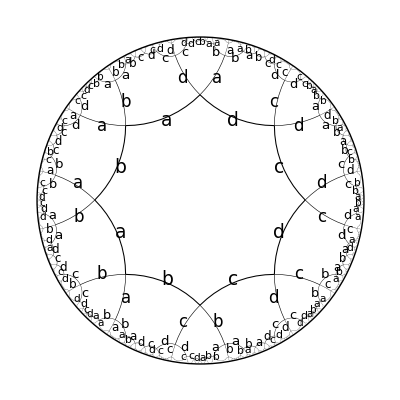

```mathematica
theta=π/2; (*interior angle of the largest octagon*)
recursionLimit=3; (*recursion limit. Don't set past 4 unless you like waiting*)
lins=draw[theta,recursionLimit];
Show[Graphics[{Circle[{0,0},1],Table[HSlinedrawArc[lins⟦i⟧,True,False],{i,1,Length[lins]}]}],ImageSize->Full]
```

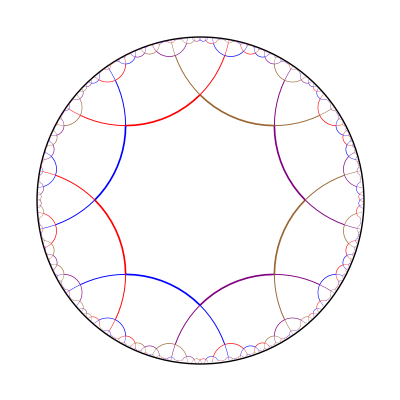

```mathematica
theta=π/2; (*interior angle of the largest octagon*)
recursionLimit=4; (*recursion limit. Don't set past 4 unless you like waiting*)
lins=draw[theta,recursionLimit];
Show[Graphics[{Circle[{0,0},1],Table[HSlinedrawArc[lins⟦i⟧,False,True],{i,1,Length[lins]}]}],ImageSize->Full]
```

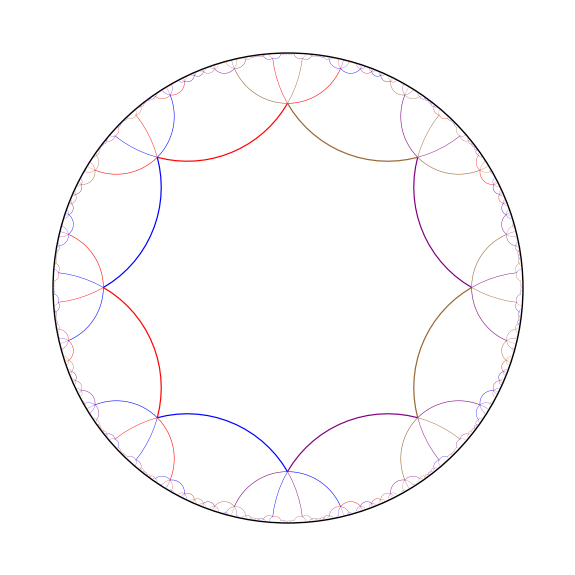

```mathematica
theta=π/3; (*interior angle of the largest octagon*)
recursionLimit=3; (*recursion limit. Don't set past 4 unless you like waiting*)
lins=draw[theta,recursionLimit];
Show[Graphics[{Circle[{0,0},1],Table[HSlinedrawArc[lins⟦i⟧,drawLabel=False],{i,1,Length[lins]}]}],ImageSize->Full]
```